# Divide and Conquer

The idea is to think about a divide and conquer mechanism for maintaining an identity plus low rank approximation for QNish optimization algorithms.

I have an existing approximation 
	B_k=α I+∑_(i=1)^m (λ_i-α)(q_i⊗q_i)
I generate one additional equation
	B_k.y_k=s_k
which I need to incorporate into the approximation.  I want:
The secant condition B_(k+1).y_k=s_k.
A parsimonious update in some sense.
No worse than m+2 distinct eigenvalues.
Some plausible mechanism to truncate the update to the m+1 form.

```mathematica
{n,m}={23,3};
Q=Orthogonalize[RandomReal[{-1,1},{m,n}]]ᵀ;
λs=RandomReal[{-1,1},m]
u=RandomReal[{-1,1},n];
A0=IdentityMatrix[n]+Q.DiagonalMatrix[λs-1].Qᵀ;
A1=A0+KroneckerProduct[u,u];
Sort[Eigenvalues[A0]]
Sort[Eigenvalues[A1]]
```

{0.645571,0.382941,0.0643041}

{0.0643041,0.382941,0.645571,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0.0692883,0.386699,0.688333,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,7.60527}

This is a new (introduced in 1981) and developing technique. The idea is to split recursively split matrices into smaller matrices.  We are again looking at a symmetric tridiagonal matrix T from a symmetric Hessenberg reduction.

An m×m symmetric tridiagonal matrix 
	T=(a_1 | b_1 |   |  
b_1 | a_2 | b_2 |  
  | b_2 | a_3 | ⋱
  |   | ⋱ | ⋱)
is irreducible if b_i≠0 for any i. Divide and conquer splits matrices by finding Q so that 
	Q.T.Qᵀ=(T_top | 0
0 | T_bot).
Splitting the matrix involves accurately solving a nonlinear equation of a very specific form.

### Splitting the Problem

Divide and conquer recursively splits a tridiagonal matrix into smaller tridiagonal matrices coupled with a rank one matrix.  An example will clarify some of this

```mathematica
SetOptions[MatrixPlot, Mesh->All,PlotLegends->Automatic];
s=4;m=2 s;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
{T1,T2}={T1Hat,T2Hat}={T⟦1;;4,1;;4⟧,T⟦5;;8,5;;8⟧};
β=T⟦s+1,s⟧;T1Hat⟦-1,-1⟧-=β; T2Hat⟦1,1⟧-=β;
THat= ArrayFlatten[({{T1Hat, 0}, {0, T2Hat}})];
vec =SparseArray[{s->1,s+1->1},m];
ROne=β KroneckerProduct[vec,vec];
TabView[{
"T"->MatrixPlot[T],
"THat"->MatrixPlot[THat],
"ROne"->MatrixPlot[ROne],
"THat+ROne"->MatrixPlot[THat+ROne]}]
```

1234

Compute the eigen decomposition of the smaller matrices
	(T̂)_1=Q_1.D_1.Q_1^ᵀ  and (T̂)_2=Q_2.D_2.Q_2^ᵀ
then if z=(Q_1⟦-1⟧ | Q_2⟦1⟧) i.e the first row of Q_2 appended to the last row of Q_1then
	T=(Q_1 |  
  | Q_2).((D_1 |  
  | D_2)+β z⊗z).(Q_1^ᵀ |  
  | Q_2^ᵀ)	
This means we can focus on the inside matrix which is diagonal plus rank one

```mathematica
s=4;m=2 s;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
{T1,T2}={T1Hat,T2Hat}={T⟦1;;4,1;;4⟧,T⟦5;;8,5;;8⟧};
β=T⟦s+1,s⟧;T1Hat⟦-1,-1⟧-=β; T2Hat⟦1,1⟧-=β;
{{λ1,Q1},{λ2,Q2}}=Map[Eigensystem,{T1Hat,T2Hat}];{Q1,Q2}=Map[Transpose,{Q1,Q2}];
z=Join[Q1⟦-1⟧,Q2⟦1⟧];
BigQ=ArrayFlatten[({{Q1, 0}, {0, Q2}})];
InsideMat = SparseArray[Band[{1,1}]->Join[λ1,λ2],{m,m}]+β KroneckerProduct[z,z];
Norm[T-BigQ.InsideMat.BigQᵀ]
```

3.62513×10^-15

If we can solve the very-very-very special inside eigenvalue problems we can recursively split our original problem.

#### Eigen values of Diagonal Plus Symmetric Rank One D+ω⊗ω

Claim: The eigenvalues of D+ω⊗ω are the roots of secular equation
	f(λ)=1+∑_(j=1)^m (ω_j)^2/(d_j-λ)=0
Argument: (D+ω⊗ω).v=λ v means 
	(D-λ Id).v=-ω (ω.v)
or equivalently 
	v+(D-λ Id)^-1 ω (ω.v)=0.
Dot this with ω to get
	ω.v+ω.(D-λ Id)^-1.ω (ω.v)=0
then factor out ω.v to get
	(ω.v)(1+ω.(D-λ Id)^-1.ω )=0
and cancel to get the secular equation
	(1+ω.(D-λ Id)^-1.ω )=0.

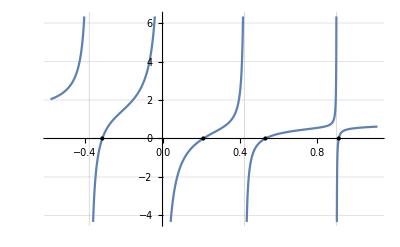

```mathematica
Clear[λ]
m=4;
{d,w}=RandomReal[{-1,1},{2,m}];
A=SparseArray[Band[{1,1}]->d,{m,m}]+KroneckerProduct[w,w];
f[λ_]:= 1+Sum[w⟦j⟧^2/(d⟦j⟧-λ),{j,1,m}];
λs=Sort[Eigenvalues[A]];
ϵ=0.2;
{a,b}={Min[Join[d,λs]],Max[Join[d,λs]]}+ϵ {-1,1};
Plot[f[λ],{λ,a,b},
Epilog->Map[Point[{#,0}]&,λs],
Exclusions->d,
GridLines->{d,Automatic}]
```

The secular equation can be solved very efficiently (using specialized variants of Newton’s Method) because of its special structure!